Define the three iterate matrices:
	1) iterate
	2) arcIterate
	3) conjIterate

```mathematica
iterateMatrix[θ_,ϕ_]:={{Cos[θ/2], -I*(E^(I*ϕ))*Sin[θ/2]},{-I*(E^(-I*ϕ))*Sin[θ/2],Cos[θ/2]}};

arcIterateMatrix[a_]:={{a, -I*Sqrt[1-a^2]},{-I*Sqrt[1-a^2], a}};

ExpZ[ϕ_]:={{E^(I*ϕ),0},{0,E^(-I*ϕ)}};
ExpX[θ_]:={{Cos[θ/2],-I*Sin[θ/2]},{-I*Sin[θ/2], Cos[θ/2]}};
conjIterateMatrix[θ_,ϕ_]:=ExpZ[-ϕ/2 ].ExpX[θ].ExpZ[ϕ/2 ];
```

Now define the sequence output given a list input

```mathematica
(*Produce final matrix given phase input list 
	for iterate Matrix*)
iterateMatrixSeq[θ_,ϕList_]:=Apply[Dot,iterateMatrix[θ,#]&/@ϕList]

(*Define a intermediate step matrix*)
Step[matrixType_,θ_,ϕ_]:=matrixType[θ].ExpZ[ϕ];

(*Produce final matrix given phase input list 
	for arcIterate Matrix*)
arcIterateMatrixSeq[a_,ϕList_]:=ExpZ[ϕList[[1]]].Apply[Dot,Step[arcIterateMatrix,a,#]&/@ϕList[[2;;]]]

(*Produce final matrix given phase input list 
	for conjIterate Matrix*)
conjIterateMatrixSeq[θ_,ϕList_]:=ExpZ[ϕList[[1]]].Apply[Dot,Step[ExpX,θ,#]&/@ϕList[[2;;]]]
```

Plot the upper left (default) with and without norm squared

```mathematica
(*All upper left plots*)
(*Plot the variation of the sequence dependent on the angle THETA
	Choose which seqType
	Choose the ϕList
	Set the parameters of the plot
	plotType: Flase -> plot Abs[]
				True -> plot Abs[]^2

*)
seqPlot[seqType_,ϕList_,{xmin_:0, xmax_:3*Pi,plotType_:False}]:=If[plotType==False,
Plot[Abs[seqType[x,ϕList][[1]][[1]]], {x,xmin,xmax}, PlotStyle->Red],
Plot[Abs[seqType[x,ϕList][[1]][[1]]]^2, {x,xmin,xmax}, PlotStyle->Green]
]

(*Plot the variation of the sequence dependent on the angle THETA
	Choose which seqType
	Choose the ϕList
	Set the parameters of the plot
	plotType: 1 -> plot Abs[]
			 2 -> plot Abs[]^2
			2 -> plot Re[]

*)
seqPlotAlt[seqType_,ϕList_,{xmin_:0, xmax_:3*Pi,plotType_:1}]:=Which[plotType==1,
Plot[Abs[seqType[x,ϕList][[1]][[1]]], {x,xmin,xmax}, PlotStyle->Red],
plotType==2,
Plot[Abs[seqType[x,ϕList][[1]][[1]]]^2, {x,xmin,xmax}, PlotStyle->Green],
plotType==3,
Plot[Re[seqType[x,ϕList][[1]][[1]]], {x,xmin,xmax}, PlotStyle->Orange]
]
```

Let’s run some examples.

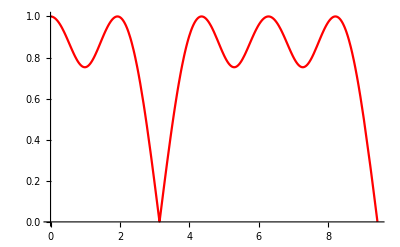

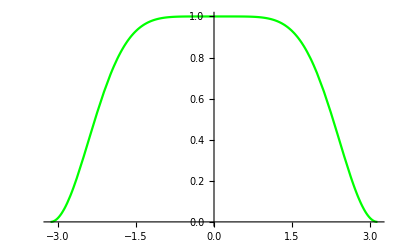

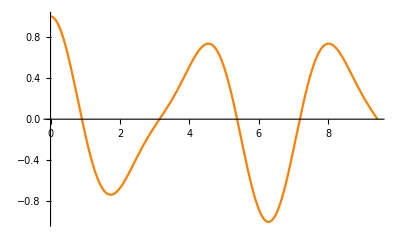

```mathematica
seqPlot[iterateMatrixSeq,{1,2,3},{0,3*Pi,False}]
seqPlot[conjIterateMatrixSeq,{π/2,-1/2 ArcCos[-1/4],ArcCos[-1/4],0,-ArcCos[-1/4],1/2 ArcCos[-1/4]},{-Pi,Pi,True}]
Manipulate[seqPlot[conjIterateMatrixSeq,{π/2,-n*ArcCos[-m],2*n*ArcCos[-m],0,-2*n*ArcCos[-m],n*ArcCos[-m]},{-Pi,Pi,True}],{n,0,2},{m,-1,1}]
seqPlotAlt[iterateMatrixSeq,{Pi,Pi/2,Pi,Pi/2,Pi},{0,3*Pi,3}]
```

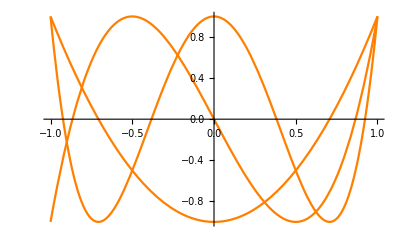

```mathematica
Show[
seqPlotAlt[arcIterateMatrixSeq,{0,0,0,0,0},{-1,1,3}],
seqPlotAlt[arcIterateMatrixSeq,{0,0,0,0},{-1,1,3}],
seqPlotAlt[arcIterateMatrixSeq,{0,0,0},{-1,1,3}]
]
```